### Functions

barbKappaModAsymp uses α=0

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
vbOverw[deltaPhi_,T_,kappa_]:=√(deltaPhi/(T (1-3/(2 kappa))));
normK[deltaPhi_,T_,kappa_]:=2/π^(1/2)(kappa^(1/2)/2 Gamma[kappa-1/2]/Gamma[kappa]+√(deltaPhi/(π T (1-3/(2kappa))))Hypergeometric2F1[1/2,kappa,3/2,-deltaPhi/(T (kappa-3/2))])^-1;
barbKappaAsymp[vpar_,vperp_,deltaPhi_,T_,kappa_]:=(1+(vpar^2+vperp^2+(vbOverw[deltaPhi,T,kappa])^2-2 (vbOverw[deltaPhi,T,kappa])(vpar^2+vperp^2)^(1/2))/kappa)^(-(kappa+1))UnitStep[vpar];qMaxF[Ep_,Tm_,kappa_]:=normK[Ep,Tm,kappa] NIntegrate[vperp barbKappaAsymp[vpar,vperp,Ep,Tm,kappa],{vpar,0,∞},{vperp,0,∞}]
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm,κ]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
(*for using peak energy*)
Ep = 945;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

```mathematica
styles[[8]]=Directive[Black,Thickness[tick]];
```

Set::noval: Symbol styles in part assignment does not have an immediate value.

```mathematica
placeList={Scaled[1.1],Below,Below,Below,Below,Below,Below,Scaled[2]};
```

```mathematica
nDigs={4,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,4}];
```

Part::partd: Part specification kappas⟦1⟧ is longer than depth of object.

Part::partd: Part specification kappas⟦2⟧ is longer than depth of object.

Part::partd: Part specification kappas⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
kapStrVals[[3]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,4}];
```

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

Set::partw: Part 8 of {κ = kappas⟦1⟧,κ = kappas⟦2⟧,κ = κ_t (≃ 2.45),κ = kappas⟦4⟧} does not exist.

## FINALE

```mathematica
kappas={1.55,1.6,1.75,2,2.45,4,10,1000};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 1.55,κ = 1.6,κ = 1.75,κ = 2,κ = κ_t (≃ 2.45),κ = 4,κ = 10,κ = 1000}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

### No labels, handle manually

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 46541.5 and 0.217422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

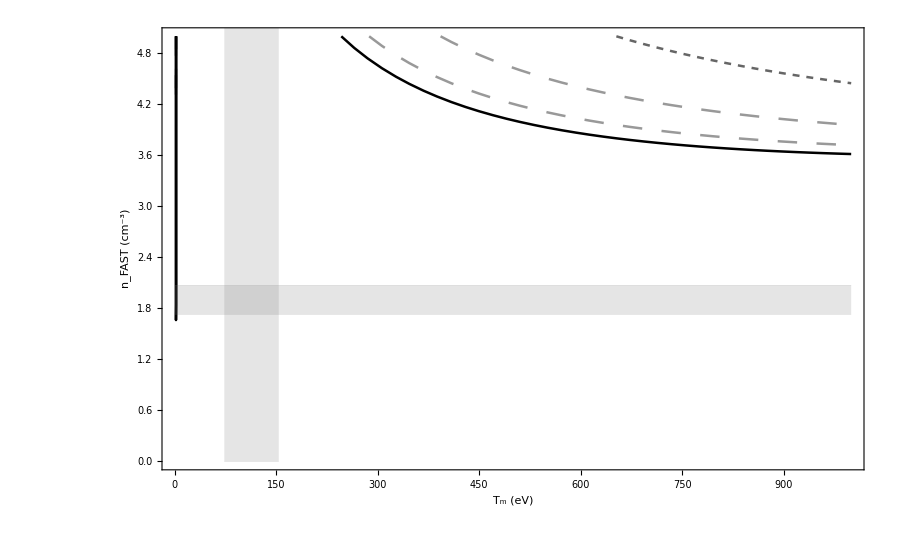

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,5}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```